# Vertical undamped spring - mass system

## Initiation

Mass :

```mathematica
m:=0.1
```

Spring constant :

```mathematica
k:=2
```

## Differential equation with initial conditions

```mathematica
equation=m y''[t]==-k y[t];
```

```mathematica
condition1=y[0]==0.2;
```

```mathematica
condition2=y'[0]==0;
```

## DSolve

```mathematica
Dsol=DSolve[{equation,condition1,condition2},y[t],t]
```

{{y[t]→0.2 Cos[4.47214 t]}}

```mathematica
Y[t_]=Dsol[[1,1,2]];
```

```mathematica
Off[Solve::ratnz]
```

```mathematica
sol=Solve[Y[period]==Y[0],period,InverseFunctions->False]
```

{{period→ConditionalExpression[1.40496 C[1],C[1]∈Integers]}}

```mathematica
T=sol[[1,1,2]]/.C[1] ->1;
```

```mathematica
ν=1/T;
```

```mathematica
ω=(2π)/T;
```

```mathematica
Grid[{{"T(s)","ν(/s)","ω(rad/s)"},{SetPrecision[T,3],SetPrecision[ν,3],SetPrecision[ω,3]}},Frame->All,ItemSize->5.5]
```

T(s) | ν(/s) | ω(rad/s)
1.4 | 0.712 | 4.47

## Animation

```mathematica
Animate[{Graphics[{
Circle[{0,0},Abs[Y[0]]],
PointSize[Large],Red,Arrow[{{0,0},{0 ,Y[t]}}],
PointSize[Large],Blue,Arrow[{{0,0},{-Y[0]  Sin[ω t ],Y[t]}}],
PointSize[Large],Red,Point[{0,Y[t]}]},PlotRange->Y[0]+0.2 Y[0],Axes->True],
Graphics[Inset[Panel[Grid[{{"t(second)","y(metre)","ϕ(radian)"},{Round[t,0.01],Round[Y[t],0.01],Round[ω t,0.01]}},Frame->All,ItemSize->5.5]]]]},{t,0,5T},AnimationRate->1,DisplayAllSteps->True,AnimationRunning->False]
```

## Equation of motion

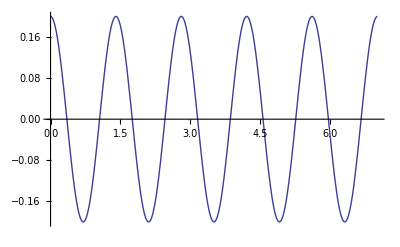

```mathematica
Plot[Y[t],{t,0,5T},PlotRange->All]
```